# Bloque 2 - Manipulaciones simbólicas

### Autor: Carlos Manuel Rodríguez Martínez Email: fis.carlosmanuel@gmail.com

## Operaciones algebraicas y cálculo

Álgebra

El lenguaje WL facilita la manipulación de elementos simbólicos. Debido a esto se pueden establecer elementos que no necesitan ser evaluados, facilitando así la posibilidad de realizar operaciones algebraicas. Es por ejemplo totalmente válido hacer

```mathematica
Clear[x]
```

```mathematica
(x+√y)^2
```

(x+√y)^2

Y realizar una operación sobre este elemento simbólico

```mathematica
Expand[(x+√y)^2]
```

x^2+2 x √y+y

Por último, la evaluación se puede realizar a través de reglas:

```mathematica
Expand[(x+√y)^2] /.{x->3,y-> 8}
```

17+12 √2

O asignando valores a las variables

```mathematica
With[{x=3,y=8},Expand[(x+√y)^2]]
```

17+12 √2

Nótese que Mathematica deja la expresión en forma simbólica, no la evalúa.

```mathematica
FullForm[17+12 √2]
```

Plus[17,Times[12,Power[2,Rational[1,2]]]]

Para forzarlo a que realice la evaluación se utiliza la función N[] que transforma la forma numérica a una expresión a atómica del tipo Real.

```mathematica
N[17+12 √2]
```

33.9706

Podemos especificarle el número de decimales que queremos

```mathematica
N[17+12 √2,20]
```

33.970562748477140586

En Mathematica hay muchas funciones numéricas predefinidas, como Sin, Cos, Tan, Log, etc...

```mathematica
Sin[5]
```

Sin[5]

```mathematica
N[Sin[5]]
```

-0.958924

Se pueden manipular expresiones algebraicas.
Para simplificar

```mathematica
Clear[x]
```

```mathematica
expresion = (x^2+1)x+6x
```

6 x+x (1+x^2)

```mathematica
FullSimplify[expresion]
```

x (7+x^2)

Para expandir

```mathematica
Expand[expresion]
```

7 x+x^3

Hay funciones para factorizar donde se puede especificar el factor

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,x]
```

3 y (2 x+x^2+x y+x^2 y^3)

```mathematica
FactorTerms[3x y^2+6y x+3y x^2+3 x^2 y^4,y]
```

3 x (2 y+x y+y^2+x y^4)

También se pueden resolver ecuaciones algebraicas. Solve[] las resuelve de manera simbólica.

```mathematica
Solve[x== 7x+9,x]
```

{{x→-3/2}}

```mathematica
Solve[Sin[x]==0.8,x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→0.927295}}

Algunas veces la manera simbólica de resolver ecuaciones no es la más eficiente,

```mathematica
Solve[Cos[x]==x,x,Reals]
```

{{x→Root[{-Cos[#1]+#1&,0.73908513321516064166}]}}

es por eso que existe la opción de resolver la ecuación numéricamente.

```mathematica
NSolve[Cos[x]==x,x,Reals]
```

{{x→0.739085}}

Para resolver ecuaciones simultáneas se hace

```mathematica
Solve[{x+y==7,4x-5y == 2},{x,y}]
```

{{x→37/9,y→26/9}}

#### Ejercicio:

Resolver el sistema de ecuaciones
Cos(x+y) = x,
y = x+2

Cálculo

Mathematica puede hacer operaciones de cálculo de manera simbólica, por ejemplo derivadas

```mathematica
D[x^7,x]
```

7 x^6

```mathematica
D[Log[Sin[Exp[x]]^2],x]
```

2 ⅇ^x Cot[ⅇ^x]

Para evaluar la derivada en algún punto se puede usar una regla de sustitución

```mathematica
N[D[Log[Sin[Exp[x]]^2],x] /. {x->8}]
```

-13589.1

De manera análoga se pueden realizar integrales

```mathematica
Integrate[7 x^6,x]
```

x^7

```mathematica
Integrate[Log[Sin[Exp[x]]^2],x]
```

-2 (-∫Log[Sin[ⅇ^x]]ⅆx+x Log[Sin[ⅇ^x]])+x Log[Sin[ⅇ^x]^2]

Se puede evaluar la integral en un intervalo. Por defecto Mathematica trata de hacerlo de manera simbólica

```mathematica
Integrate[7 x^6,{x,5,6}]
```

201811

Sin embargo no siempre tiene éxito.

```mathematica
Integrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

∫_0.5^1 Log[Sin[ⅇ^x]^2]ⅆx

En éstos casos es necesario realizar la integral numéricamente.

```mathematica
NIntegrate[Log[Sin[Exp[x]]^2],{x,0.5,1}]
```

-0.244913

#### Ejercicio 1:

Verificar si se cumple el teorema fundamental del cálculo en las funciones de Mathematica.

#### Ejercicio 2:

Encontrar la solución numérica a la ecuación

∫√(x+√x)dx= x donde x ∈ Reales

#### Ejercicio 3:

Obtener dos listas con la primera y segunda derivada de las siguientes funciones:

```mathematica
funciones = {ⅇ^x,x^2,Log[x],Sin[x],ArcTan[x],Cosh[x], ArcCosh[x],ChebyshevT[n, x],EllipticE[x],BesselJ[0,x]};
```

Después crear una tabla con funciones y su primera y segunda derivada utilizando la función Grid[].

Proyecto: Eigen-estados cuánticos de un potencial bidimensional

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

-Graphics-

El objetivo del proyecto es implementar el método de expansión utilizando un potencial con una geometría complicada (triángulo, polígono, círculo cortado, etc.. )

El proyecto se dividirá en los siguietes pasos.

1. Primero es necesario establecer la base sobre la cual se construye el método de expansión. Para este proyecto será dada la base y la función para calcular los elementos de la matriz ν.

```mathematica
ϕm[x_,y_,a1_,a2_,{m1_,m2_}]:=√(2/a1) Sin[(π m1 x)/a1] √(2/a2) Sin[(π m2 y)/a2];
ν[k1_,k2_,a1_,a2_,base_,regionII_]:=Module[{x,y},
Quiet[NIntegrate[ϕm[x,y,a1,a2,Part[base,k1]]  ϕm[x,y,a1,a2,Part[base,k2]],{x,y}∈regionII,Method->"MonteCarlo"]]
];

MSize = 5;
baseIndexes=Flatten[Table[{m1,m2},{m1,1,MSize},{m2,1,MSize}],1];
```

Nótese que la integral se realiza sobre una región definida como regionII. Comencemos entonces definiendo la región. Dada una regiónI, ¿cómo podemos definir la regiónII? Por simplicidad hagamos primero que

```mathematica
regionI = Disk[]
```

2. Ya tenemos la regiónII, ahora es necesario encontrar los valores de a1 y a2.

3. Es la hora de hacer el cálculo más tardado del proyecto, construir la matriz νnm. Aquí son especialmente útiles los índices de la base.

4. Calcular δCoeff y δnm tal que se pueda construir la matriz del hamiltoniano dada por:

5. Obtener las energías En y los eigenvectores cm.

6. Por último, graficar la norma al cuadrado de la función de onda de cada eigenestado. Esto nos da la densidad de probabilidad de encontrar a la partícula en un punto determinado.

```mathematica
ψ[x_,y_,a1_,a2_,eigenstate_,base_,cm_]:=Sum[cm[[eigenstate,k]] ϕm[x,y,a1,a2,Part[base,k]],{k,1,Length[base]}];
```

```mathematica
Hnm = δCoeff*δnm + V0*νnm;
```

Un ejemplo del tipo de gráfica que se espera es el siguiente.

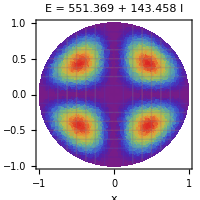

#### Solución

```mathematica
Needs["AdvancedMapping`"];
```

```mathematica
ϕm[x_,y_,a1_,a2_,{m1_,m2_}]:=√(2/a1) Sin[(π m1 x)/a1] √(2/a2) Sin[(π m2 y)/a2];
ν[k1_,k2_,a1_,a2_,base_,regionII_]:=Module[{x,y},
Quiet[NIntegrate[ϕm[x,y,a1,a2,Part[base,k1]]  ϕm[x,y,a1,a2,Part[base,k2]],{x,y}∈regionII,Method->"MonteCarlo"]]
];
```

```mathematica
GetRegionDimensions[region_]:=Map[Abs[Apply[Subtract,#]]&,RegionBounds[region]];
CalculateEigenstates[regionI_,MSize_]:=Module[
{regionIBoundingBox,regionII,base,νnm,δnm,k1,k2,δCoeff,Hnm,En,cm,a1,a2,ℏ = 1,m = 1,V0 = 200000,Δ = 0.000001},

regionIBoundingBox = Apply[Rectangle,Transpose[RegionBounds[regionI]]+{Δ,-Δ}];
regionII = RegionDifference[regionIBoundingBox,regionI];

base=Flatten[Table[{m1,m2},{m1,1,MSize},{m2,1,MSize}],1];
{a1,a2} = GetRegionDimensions[regionI];
νnm = ProgressTable[ν[k1,k2,a1,a2,base,regionII],{k1,1,Length[base]},{k2,1,Length[base]},"ShowInfo"->True];
δnm = IdentityMatrix[Length[base]];

δCoeff = Table[(ℏ^2 π^2)/(2 m)Total[Part[base,k]^2/{a1,a2}^2],{k,1,Length[base]}];
Hnm = δCoeff*δnm + V0*νnm;
En = Sort[Eigenvalues[Hnm]];
cm = Part[Eigenvectors[Hnm],Ordering[Eigenvalues[Hnm]]];
Return[{a1,a2,base,En,cm,Hnm}];
];
```

```mathematica
ψ[x_,y_,a1_,a2_,eigenstate_,base_,cm_]:=Sum[cm[[eigenstate,k]] ϕm[x,y,a1,a2,Part[base,k]],{k,1,Length[base]}];
```

```mathematica
regionI = Disk[];
{a1,a2,base,En,cm,Hnm} = CalculateEigenstates[regionI,3];
```

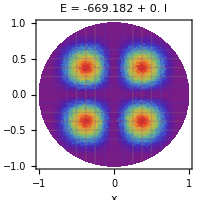
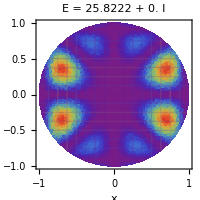
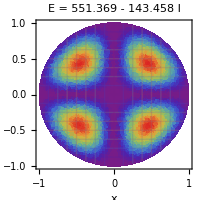
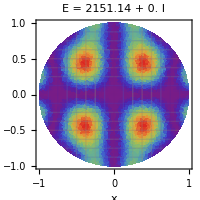
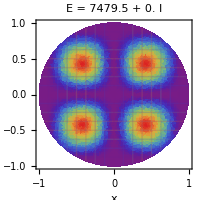
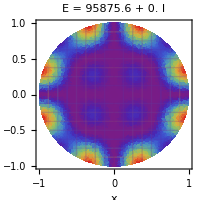
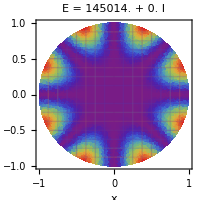
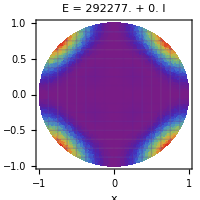
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[
DensityPlot[Abs[ψ[x,y,a1,a2,eigenstate,base,cm]]^2,{x,y}∈regionI,
Axes->True,
FrameLabel->{"x", "y"},
AxesOrigin->{1,1},
ColorFunction->"Rainbow",
Mesh->Automatic,
ImageSize->200,
PerformanceGoal->"Quality",
PlotLabel->StringJoin["E = ",ToString[En[[eigenstate]]]],
PlotRange->All,
PlotPoints->35
]
,
{eigenstate,1,Length[base]}
]
```

## Introducción a las gráficas

Introducción

WL es un lenguaje de naturaleza simbólica, eso significa que no hace distinción entre un tipo de datos numérico como un entero, y un gráfico. La capacidad de mezclar elementos de cualquier tipo es una de sus características más poderosas ya que resulta relativamente fácil implementar gráficos con elementos interactivos, valores numéricos y todo tipo de funcionalidades.

La función gráfica más elemental es Graphics[], de la cual se derivan todos los demás elementos gráficos. Graphics trabaja con elementos simples denominados primitivas, por ejemplo:

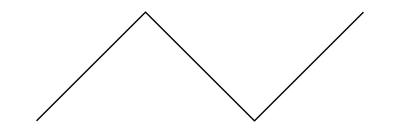

```mathematica
Graphics[Line[{{1,0},{2,1},{3,0},{4,1}}]]
```

Es posible combinar varias primitivas:

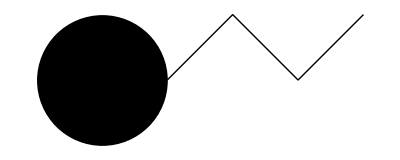

```mathematica
Graphics[{Disk[],Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Y establecer directivas para cada una de las primitivas:

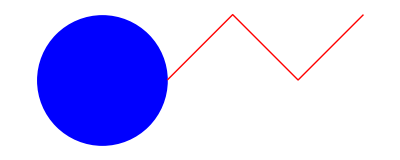

```mathematica
Graphics[{Blue,Disk[],Red,Thick,Line[{{1,0},{2,1},{3,0},{4,1}}]}]
```

Gráficas de funciones

Para efectos práctivos uno no suele utilizar las primitivas básicas ya que existen funciones que crean elementos gráficos de forma adecuada para graficar funciones. La gráfica más simple se puede crear con una función Plot, que grafica funciones definidas en los números reales.

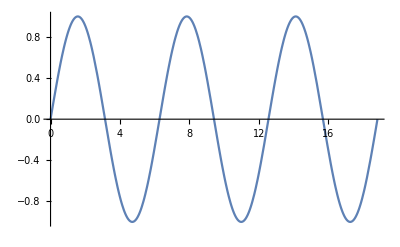

```mathematica
Plot[Sin[x],{x,0,6π}]
```

Para aumentar la cantidad de detalles que se muestra en la gráfica se pueden utilizar argumentos opcionales

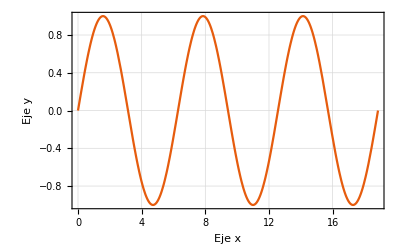

```mathematica
Plot[Sin[x],{x,0,6π},PlotTheme->"Scientific",FrameLabel->{"Eje x","Eje y"},GridLines->Automatic]
```

Algunas funciones discontinuas no se pueden graficar adecuadamente con Plot, para esto está DiscretePlot

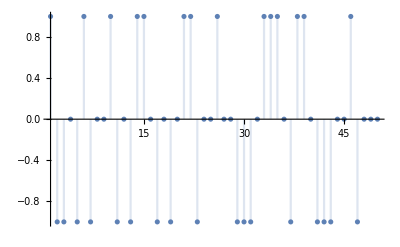
-Graphics--Graphics-

```mathematica
Row[{Plot[MoebiusMu[k],{k,1,50},ImageSize->400],DiscretePlot[MoebiusMu[k],{k,1,50},ImageSize->400]}]
```

Se pueden agrupar varias gráficas

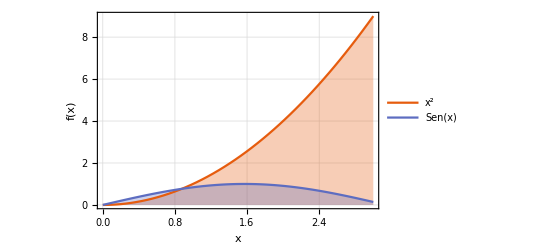

```mathematica
Plot[{x^2,Sin[x]},{x,0,3},PlotTheme->"Scientific", FrameLabel->{"x","f(x)"},ImageSize->400,BaseStyle->FontSize->16,GridLines->Automatic,Filling->Bottom,PlotLegends->{"x^2","Sen(x)"}]
```

Combinar gráficas a veces es útil para crear efectos

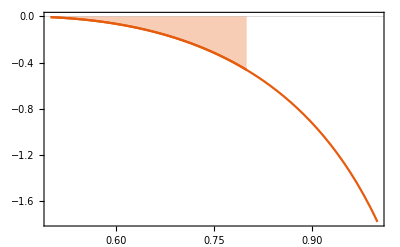

```mathematica
Show[
Plot[Log[Sin[Exp[x]]^2],{x,0.5,1},PlotTheme->"Scientific"],
Plot[Log[Sin[Exp[x]]^2],{x,0.5,0.8},Filling->Top,PlotTheme->"Scientific"]
]
```

Existen más tipos de gráficas que se pueden realizar, como gráficas en 3d

```mathematica
Plot3D[Sin[x+y^2],{x,-3,3},{y,-2,2},PlotTheme->"Scientific", AxesLabel->{"x","y","z"},BaseStyle->FontSize->16]
```

-Graphics3D-

Se pueden realizar gráficas implícitas. Nótese que la intersección coincide con la solución.

{{x→4.11111,y→2.88889}}

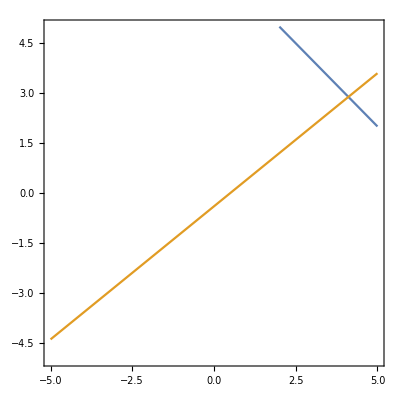

```mathematica
N[Solve[{x+y==7,4x-5y == 2},{x,y}]]
ContourPlot[{x+y==7,4x-5y == 2},{x,-5,5},{y,-5,5}]
```

#### Ejercicio 1:

Graficar

cos(x+y) = x,
y = x+2

y comprobar que la intersección coincide con la solución del sistema de ecuaciones.

Elementos interactivos

```mathematica
Manipulate[i^2,{i,0,10}]
```

```mathematica
Manipulate[
Plot[{x^2,Sin[a x]},
{x,0,3},
PlotTheme->"Scientific",
 FrameLabel->{"x","f(x)"},
ImageSize->400,
BaseStyle->FontSize->16,
GridLines->Automatic,
Filling->Bottom,
PlotLegends->{"x^2","Sen(ax)"}
],
{a,1,5}
]
```

#### Ejercicio

Crear un elemento interactivo que encuentre la solución de
Cos(x+y) = ax,
y = x+2,
donde a es un elemento variable de 1 a 2.